# Examen 2: Parte Computacional Sistemas Dinámicos No Lineales

## Profesor: Josué Manik Nava Sedeño Alumno: Wei Le Hu Tang 28 de abril del 2024

## 1. Discute las bifurcaciones que ocurren en el sistema, y dibuja el diagrama de bifurcación

## para varios valores de μ donde se puedan ver todos los comportamientos cualitativamente diferentes que encontraste en el examen teórico.

Como  es constante, entonces sólo pueden haber soluciones de espiral y ciclos límite dependientes de los puntos fijos de 
Las soluciones de  son 
Como , las soluciones  y  sólo existen si , pero 
Por otro lado , entonces 

Discusión de casos:

es una espiral inestable

#### Estabilidades

es una espiral inestable,
 es un ciclo estable,
 es un ciclo inestable

#### Estabilidades

es una espiral inestable,
 es un ciclo semiestable por la izquierda

#### Estabilidades

es una espiral inestable,
 es un ciclo estable,
 es un ciclo inestable

### Retrato fase del sistema dado μ

```mathematica
Clear["Global`*"]

dr1[r_,μ_]=r(μ-r)(μ-r^2);

(*conversión de polares a cartesianas*)
polarToCartesian[{r_,θ_}]:=r*{Cos[θ],Sin[θ]};
s1=ParametricNDSolve[{r'[t]==dr1[r[t],μ],θ'[t]==-1,r[0]==r0,θ[0]==θ0},{r,θ},{t,0,1000},{r0,θ0,μ}];
solution1[r0_,θ0_,μ_,t_]:=Evaluate[{r[r0,θ0,μ][t],θ[r0,θ0,μ][t]}/. s1];
```

```mathematica
M=3;
Manipulate[Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{dr1[r,μ],-1},{r,θ}->{x,y}],{x,-M,M},{y,-M,M},StreamColorFunction->None,StreamStyle->Gray],
(*solución cercana al cero, fuera del ciclo más grande, y entre los dos ciclos, respectivamente*)
ParametricPlot[polarToCartesian[solution1[0.05,0,μ,t]],{t,0,10},PlotStyle->{Purple,Thick}],
ParametricPlot[If[0.05<μ,polarToCartesian[If[μ<1,solution1[Sqrt[μ]+0.05,0,μ,t],solution1[μ+0.05,0,μ,t]]]],{t,0,30},PlotStyle->{Pink,Thick}],
ParametricPlot[If[0.05<μ,polarToCartesian[If[μ<1,solution1[Sqrt[μ]-0.05,0,μ,t],solution1[μ-0.05,0,μ,t]]]],{t,0,30},PlotStyle->{Red,Thick}],
(*ciclos limite de radios μ y √μ, respectivamente*)
ParametricPlot[If[0<μ,{μ Cos[t],μ Sin[t]}],{t,0,2*Pi},PlotStyle->{Blue,If[μ<1,Thick,Dashed]},PlotLegends->{""}],
ParametricPlot[If[0<μ,{Sqrt[μ] Cos[t],Sqrt[μ] Sin[t]}],{t,0,2*Pi},PlotStyle->{Green,If[μ<1,Dashed,Thick]},PlotLegends->{""}]}],
{μ,-1,2}]
```

### Diagrama de bifurcación de dado μ

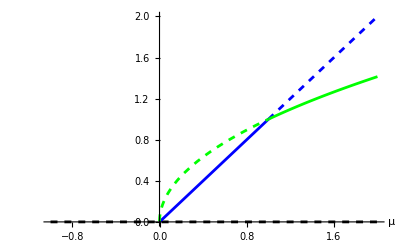

```mathematica
Plot[{0,If[0<=μ<=1,μ],If[0<=μ<=1,Sqrt[μ]],If[1<μ,μ],If[1<μ,Sqrt[μ]]},{μ,-1,2},PlotStyle->{{Black,Dashed},{Blue},{Green,Dashed},{Blue,Dashed},{Green}},AxesLabel->{"μ",""},PlotLegends->{"","",""}]
```

En  hay una bifurcación de tridente para , o bien de Hopf viendo el sistema completo; y en  hay una bifurcación transcrita, pues  y  cambian de estabilidad

## 2. Grafica el retrato fase del sistema

## y dibuja sobre éste CON LÍNEAS CLARAS Y COLORES DISTINGUIBLES las soluciones que forman el grafo cíclico, encontrando sus soluciones numéricas y graficándolas sobre el espacio fase. Grafica también la componente como función del tiempo de una solución numérica al sistema con condiciones iniciales , con el eje horizontal en escala logarítmica, hasta al menos .

```mathematica
Clear["Global`*"]

dr2[r_,θ_]=r(1-r^2)((r Sin[θ])^2+((r Cos[θ])^2 -1)^2);
dθ2[r_,θ_]=(r Sin[θ])^2+((r Cos[θ])^2 -1)^2;
(*conversión de polares a cartesianas*)
polarToCartesian[{r_,θ_}]:=r*{Cos[θ],Sin[θ]};
s2=ParametricNDSolve[{r'[t]==dr2[r[t],θ[t]],θ'[t]==dθ2[r[t],θ[t]],r[0]==r0,θ[0]==θ0},{r,θ},{t,0,1000},{r0,θ0}];
solution2[r0_,θ0_,t_]:=Evaluate[{r[r0,θ0][t],θ[r0,θ0][t]}/. s2];
```

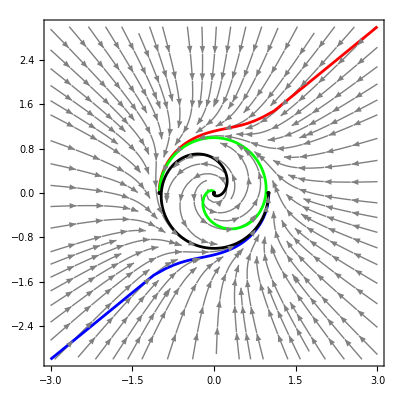

```mathematica
M=3;
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{dr2[r,θ],dθ2[r,θ]},{r,θ}->{x,y}],{x,-M,M},{y,-M,M},StreamColorFunction->None,StreamStyle->Gray,Epilog->{PointSize[Large],Point[{{-1,0},{0,0},{1,0}}]}],
(*distintas soluciones del sistema*)
ParametricPlot[{polarToCartesian[solution2[Sqrt[2*M^2],Pi/4,t]],
polarToCartesian[solution2[Sqrt[2*M^2],5Pi/4,t]],
polarToCartesian[solution2[0.01,Pi/6,t]],
polarToCartesian[solution2[10^(-9),Pi/4,t]]},
{t,0,100},PlotStyle->{Red,Blue,Green,Black},PlotLegends->{"","","",""}]}]
```

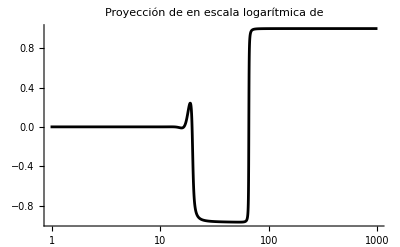

```mathematica
s22=NDSolve[{r'[t]==dr2[r[t],θ[t]],θ'[t]==dθ2[r[t],θ[t]],r[0]==10^(-9),θ[0]==Pi/4},{r[t],θ[t]},{t,0,1000}];
x[t_]=r[t]Cos[θ[t]];

LogLinearPlot[x[t]/. s22,{t,0,1000},PlotStyle->Black,AxesLabel->{"",""},PlotLabel->"Proyección de  en escala logarítmica de "]
```

## 3. Dibuja el retrato fase del sistema

## Identifica las cuencas de atracción de los equilibrios estables graficando numéricamente las soluciones separatrices que las delimitan (nota: puede tomar algunos intentos definir el tiempo adecuado para las condiciones iniciales)

### Ceroclinas

### Puntos de equilibrio

### Retrato fase

ParametricNDSolve::ndsz: At t == 0.115901, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {1.×10^6} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

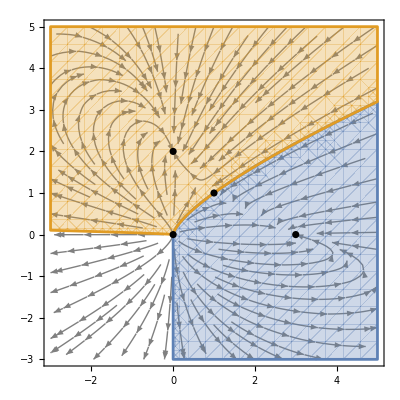

```mathematica
Clear["Global`*"]
dx[x_,y_]=x(3-x-2y);
dy[x_,y_]=y(2-x-y);

(*solución paramétrica numérica*)
s3=ParametricNDSolve[{x'[t]==dx[x[t],y[t]],y'[t]==dy[x[t],y[t]],x[0]==x0,y[0]==y0},{x,y},{t,0,1000000},{x0,y0}];
sol3[x0_,y0_,t_]:=Evaluate[{x[x0,y0][t],y[x0,y0][t]}/. s3];

err=0.0001;
M=5;
m=-3;
Show[StreamPlot[{dx[x,y],dy[x,y]},{x,m,M},{y,m,M},StreamColorFunction->None,StreamStyle->Gray],
ParametricPlot[sol3[-0.5,-0.5,t],{t,0,100}], (*Por alguna razón, si no tengo esta parametrización, la siguiente linea de código no funciona*)
(*Se grafican las cuencas de atracción usando como condición que, dado el punto inicial, la distancia euclideana del punto de equilibrio y la solución al tiempo  se menor que la variable err*)
RegionPlot[{EuclideanDistance[sol3[x,y,1000000],{3,0}]<=err,EuclideanDistance[sol3[x,y,1000000],{0,2}]<=err},{x,m,M},{y,m,M}],
(*puntos de equilibrio*)
ListPlot[{{0,0},{0,2},{3,0},{1,1}}, PlotStyle->Black]
]
```